# Fonction de Van der Waerden

```mathematica
α[x_]:=Floor[x+0.5]
```

```mathematica
δ[x_]:=Abs[x-α[x]]
```

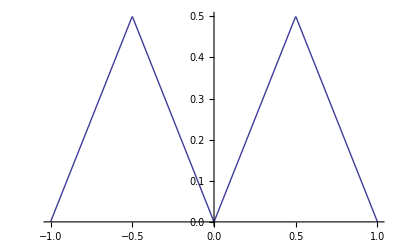

```mathematica
Plot[δ[x],{x,-1,1}]
```

```mathematica
f[x_,n_]:=Sum[δ[2^k*x]/2^k,{k,0,n}]
```

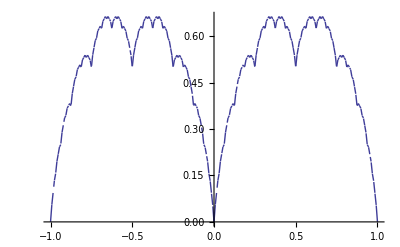

```mathematica
Plot[f[x,6],{x,-1,1}]
```

```mathematica
Plot3D[f[x,3]*f[y,3],{x,0,1},{y,0,1}]
```

-Graphics3D-